# Problem Set 4

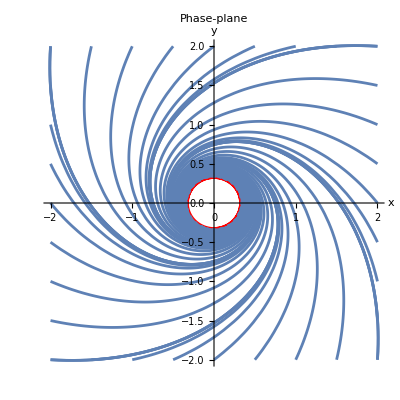

```mathematica
maxt = 10;
μ = 0.1;
ω = 1.0;
ν = 1.0;

sol[x0_, y0_] := NDSolve[{x'[t] == μ*x[t] - ν*y[t]^3 - x[t]*y[t]^2 - ν*x[t]^2*y[t] - ω*y[t] - x[t]^3, 
								y'[t] == ω*x[t] + μ*y[t] + ν*x[t]*y[t]^2 + ν*x[t]^3 - y[t]^3 - x[t]^2*y[t], 
								x[0]==x0, y[0]==y0},
								{x,y},
								{t,0,maxt}]
sol[x0_, y0_] := NDSolve[
  {
    x'[t] == μ*x[t] - ν*y[t]^3 - x[t]*y[t]^2 - ν*x[t]^2*y[t] - ω*y[t] - x[t]^3,
    y'[t] == ω*x[t] + μ*y[t] + ν*x[t]*y[t]^2 + ν*x[t]^3 - y[t]^3 - x[t]^2*y[t],
    x[0] == x0,
    y[0] == y0
  },
  {x, y},
  {t, 0, maxt}
]

minx=-2;
miny=-2;
maxx=2;
maxy=2;
step = 0.5;
initialC=Join[
			Table[{minx,y},{y,miny,maxy,step}],
			Table[{maxx,y},{y,miny,maxy,step}],
			Table[{x,miny},{x,minx,maxx,step}],
			Table[{x,maxy},{x,minx,maxx,step}]];
solLC = NDSolve[
  {
    x'[t] == μ*x[t] - ν*y[t]^3 - x[t]*y[t]^2 - ν*x[t]^2*y[t] - ω*y[t] - x[t]^3,
    y'[t] == ω*x[t] + μ*y[t] + ν*x[t]*y[t]^2 + ν*x[t]^3 - y[t]^3 - x[t]^2*y[t],
    x[0] == N[Sqrt[μ]],
    y[0] == 0
  },
  {x, y},
  {t, 0, 100}
];
p1=Show[
	Table[
		ParametricPlot[
			Evaluate[{x[t],y[t]}/. sol[initialC⟦i,1⟧, initialC⟦i,2⟧]],
			{t,0,maxt},
			PlotRange->{{minx,maxx},{miny,maxy}},
			AxesLabel->{x,y}
		]
		/. Line[x_]:>{Arrowheads[{{0.05, 0.5}, {0.05, 0.0}}],Arrow[x]},{i,1,Length[initialC]}
	], 
	ParametricPlot[
	    Evaluate[{x[t], y[t]} /. solLC], 
	    {t, 90, 100}, 
	    PlotStyle -> {Red, Thick}
	  ],
	PlotLabel -> "Phase-plane"
]
```

```mathematica
Jt ={
   {(-4/10 * Pi)/(11/10), 0},
   {(4 * Sqrt[1/10] * Pi)/(11/10), 0}
}
M = MatrixExp[(Jt)]
```

{{-(4 π)/11,0},{(4 √10 π)/11,0}}

{{ⅇ^(-4 π/11),0},{√10 ⅇ^(-4 π/11) (-1+ⅇ^(4 π/11)),1}}